```mathematica
(*Approximation de la probabilité de ruine ultime*)
(*Developpement de densité de probabilité bivariée*)
(*La mesure de référence choisi est la loi Gamma de paramètre ξ et ν*)
muGamma=Function[{x,m,r},(1/m)^(r)*Exp[-x/m]*x^(r-1)/Gamma[r]];
(*Polynôme mu orthogonaux associé*)
QnGamma=Function[{n,x,m,r},(-1)^n*LaguerreL[n,r-1,x/m]/Sqrt[Binomial[n+r-1,n]]];
(*Loi binomial negative de paramètre a et p*)
FoncGenPoisson=Function[{s,λ},Exp[λ(s-1)]-Exp[-λ]];
(*Distribution Gamma*)
LaplaceUnif=Function[{s,α,β},(Exp[s*β]-Exp[s*α])/(β-α)/s];;
LaplaceCompoundPoissonUnif=Function[{s,λ,α,β},FoncGenPoisson[LaplaceUnif[s,α,β],λ]];
CoefGenFunctionCompoundPoissonUnif=Function[{λ,α,β,z,m,r},FullSimplify[(1+z)^(-r)*LaplaceCompoundPoissonUnif[z/m/(1+z),λ,α,β]]];
ExpansionCoefficientCompoundPoissonUnif=Function[{λ,α,β,z,m,r,K},Expansion=Normal[Series[CoefGenFunctionCompoundPoissonUnif[λ,α,β,z,m,r],{z,0,K}]];Table[1/Sqrt[Binomial[i+r-1,i]]/(i!)*(D[Expansion,{z,i}]/.z->0),{i,0,K}]];
(*Système de polynômes orthogonaux*)
Qnm=Function[{x,m,r,K},Table[QnGamma[i,x,m,r]muGamma[x,m,r],{i,0,K}]];
DensityExpansion=Function[{VectorCoef,x,m,r,K},Total[VectorCoef[[1;;K+1]]*Qnm[x,m,r,K]]];
SurvivalExpansion=Function[{VectorCoef,u,m,r,K},Integrate[DensityExpansion[VectorCoef,x,m,r,K],{x,u,+∞},Assumptions->Im[u]≠0||Re[u]>0]]
(*Evaluation de la probabilité de ruine via ls FFT*)
(*Fonction de survie via les FFT*)
(*Calcul des Sn*)
FoncGenPoissonFFT=Function[{s,λ},Exp[λ(s-1)]];
LaplaceCompoundPoissonUnifSurvival=Function[{s,λ,α,β},(1-FoncGenPoissonFFT[LaplaceUnif[-s,α,β],λ])/s];
SnCompoundPoissonUnifSurvival=Function[{b,u,n,λ,α,β},Exp[b/2]/2/u*Re[LaplaceCompoundPoissonUnifSurvival[b/2/u,λ,α,β]]+Exp[b/2]/u*Sum[(-1)^(i)*Re[LaplaceCompoundPoissonUnifSurvival[(b+I*i*2π)/2/u,λ,α,β]],{i,1,n,1}]];
SurvivalCompoundPoissonUnifFFT=Function[{m,b,u,n,λ,α,β},Sum[Binomial[m,i]*2^(-m)SnCompoundPoissonUnifSurvival[b,u,n+i,λ,α,β],{i,0,m,1}]];
(*Evaluation de la probabilité de ruine via la scaled laplace Transform*)
LaplaceCompoundPoissonUnifMnats=Function[{s,λ,α,β},FoncGenPoissonFFT[LaplaceUnif[-s,α,β],λ]];
(*Formule de la densité et transformée de Laplace de la probabilité de ruine*)
SurvivalCompoundPoissonUnifMnats=Function[{λ,α,β,αMnats,bMnats,u},LaplaceCompoundPoissonUnif=Table[LaplaceCompoundPoissonUnifMnats[Log[bMnats]*j,λ,α,β],{j,1,αMnats}];LaplaceCompoundPoissonUnif=PrependTo[LaplaceCompoundPoissonUnif,1];
Sum[
Sum[
Binomial[αMnats,j]*Binomial[j,k](-1)^(j-k)LaplaceCompoundPoissonUnif[[j+1]]
,{j,k,αMnats}]
,{k,0,Floor[αMnats*Exp[-u*Log[bMnats]]]}
]];
DensityCompoundPoissonGammaMnats=Function[{λ,α,β,αMnats,bMnats,x},
Floor[αMnats*Exp[-Log[bMnats]*x]]Log[bMnats]Gamma[αMnats+2]/(αMnats*Gamma[Floor[αMnats*Exp[-Log[bMnats]*x]]+1])*
Sum[
(-1)^(j)*LaplaceCompoundPoissonUnifMnats[j+Floor[αMnats*Exp[-Log[bMnats]*x]],λ,α,β]/j!/(αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]-j)!
,{j,0,αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]}]
];
SurvivalCompoundPoissonGammaMnatsBis=Function[{λ,α,β,αMnats,bMnats,x},
Floor[αMnats*Exp[-Log[bMnats]*x]]Log[bMnats]Gamma[αMnats+2]/(αMnats*Gamma[Floor[αMnats*Exp[-Log[bMnats]*x]]+1])*
Sum[
(-1)^(j)*LaplaceCompoundPoissonUnifMnats[j+Floor[αMnats*Exp[-Log[bMnats]*x]],λ,α,β]/j!/(αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]-j)!
,{j,0,αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]}]
];

(*Algorithme de Panjer*)
(*Discrétisation, h représente le pas de discrétisation, u est la limite, on créer un vecteur de taille u/h*)
DiscretizeUnif=Function[{α,β,umax,h},PartitionGrid=Table[k*h,{k,0,umax/h,1}];ProbaU=Table[N[CDF[UniformDistribution[{α,β}],Max[PartitionGrid[[i]]+h/2,0]]-CDF[UniformDistribution[{α,β}],Max[PartitionGrid[[i]]-h/2,0]]],{i,1,Length[PartitionGrid](*-1*),1}]];
ProbaDiscretePoissonCompoundUnif=Function[{λ,h,VectProbaU,umax},ProbaCompoundPoisson={};AppendTo[ProbaCompoundPoisson,Exp[-λ]];
For[j=1,j<umax/h+1,j++,AppendTo[ProbaCompoundPoisson,Sum[λ*k/j*VectProbaU[[k]]*ProbaCompoundPoisson[[(j-k)+1]],{k,1,j,1}]]];ProbaCompoundPoisson];
SurvivalPoissonCompoundUnifPanger=Function[{VectProbaCompoundPoisson,h,u},1-Sum[VectProbaCompoundPoisson[[k]],{k,1,u/h}]];
```

Function[{VectorCoef,u,m,r,K},Integrate[DensityExpansion[VectorCoef,x,m,r,K],{x,u,+∞},Assumptions→Im[u]≠0||Re[u]>0]]

```mathematica
(*Sinistres de loi Uniforme*)
α=0;
β=10;
(*Fréquence des sinistres de loi de Poisson*)
λ=3;
μX=λ*Mean[UniformDistribution[{α,β}]];
VarX=λ*Mean[UniformDistribution[{α,β}]]+Moment[UniformDistribution[{α,β}],2]*λ;
μU=Mean[UniformDistribution[{α,β}]];
VarU=Variance[UniformDistribution[{α,β}]];
NbParametrization=4;
m={VarU/μU,(β-α)/2,μX,VarX/μX}
r={μU^(2)/VarU,1,1,μX^(2)/VarX}
(*Fonction génératrice des coefficients*)
(*CoefGenFunctionCompoundPoissonUnif[λ,α,β,z,m,r]*)
```

{5/3,5,15,23/3}

{3,1,1,45/23}

```mathematica
(*Coefficients et polynômes orthogonaux*)
KPoly=75;
MatrixForm[N[VectorCoef=
Table[ExpansionCoefficientCompoundPoissonUnif[λ,α,β,z,m[[i]] ,r[[i]],KPoly],{i,1,NbParametrization}]]]
(*Matrice des polynomes multipliés par leur mesure*)
MatrixForm[DensityCompoundPoissonUnifPolynomial=Table[DensityExpansion[VectorCoef[[i]],x,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]];
MatrixForm[SurvivalCompoundPoissonUnifPolynomial=Table[SurvivalExpansion[VectorCoef[[i]],u,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]];
```

(0.950213 | 3.55034 | 11.5131 | 31.1478 | 74.4977 | 159.342 | 310.751 | 557.506 | 928.748 | 1445.66 | 2114.35 | 2918.06 | 3814.89 | 4738.67 | 5608.36 | 6338.6 | 6855.47 | 7107.64 | 7075.27 | 6771.56 | 6238.89 | 5539.21 | 4744.33 | 3922.95 | 3134.34 | 2421.28 | 1809.57 | 1309.11 | 917.266 | 622.499 | 409.683 | 261.182 | 161.572 | 96.9616 | 56.3605 | 31.8351 | 17.5084 | 9.14424 | 4.90581 | 2.30298 | 1.17183 | 0.591074 | 0.188809 | 0.126847 | 0.103547 | -0.0992633 | 0.139065 | -0.0818385 | 0.00588199 | 0.0630317 | -0.0764268 | 0.0262941 | 0.0620581 | -0.139252 | 0.161608 | -0.115977 | 0.0278287 | 0.053209 | -0.0818149 | 0.0429966 | 0.0394802 | -0.117107 | 0.144852 | -0.107109 | 0.0263728 | 0.0501979 | -0.0782731 | 0.0418139 | 0.0381305 | -0.116048 | 0.148323 | -0.117932 | 0.0434017 | 0.0326296 | -0.0681332 | 0.0452188
0.950213 | 2.04979 | 1.45021 | 0.0497871 | -0.274787 | 0.0331204 | 0.0591415 | -0.0383082 | 0.00933826 | 0.000458365 | -0.000238382 | -0.000467661 | -0.000979516 | 0.00369795 | -0.00639534 | 0.00836184 | -0.00937907 | 0.00944778 | -0.00863693 | 0.00704651 | -0.00481371 | 0.00211898 | 0.00082027 | -0.00376589 | 0.00647931 | -0.00874181 | 0.0103721 | -0.0112399 | 0.0112753 | -0.0104725 | 0.00888931 | -0.00664083 | 0.00389 | -0.000834237 | -0.00230984 | 0.00532272 | -0.00799791 | 0.0101564 | -0.0116585 | 0.0124127 | -0.0123805 | 0.0115772 | -0.0100692 | 0.00796732 | -0.005418 | 0.00259168 | 0.000329456 | -0.00316418 | 0.00574414 | -0.00792433 | 0.00959145 | -0.0106696 | 0.0111233 | -0.0109575 | 0.0102147 | -0.00897026 | 0.00732539 | -0.00539895 | 0.00331873 | -0.00121266 | -0.000799376 | 0.00261257 | -0.00414276 | 0.00533018 | -0.00614131 | 0.00656885 | -0.00662991 | 0.00636276 | -0.0058224 | 0.00507532 | -0.00419403 | 0.00325154 | -0.00231634 | 0.00144806 | -0.000694202 | 0.0000879174
0.950213 | 0.0497871 | -0.327565 | 0.309046 | -0.200713 | 0.0918996 | -0.0130121 | -0.0325234 | 0.0515901 | -0.0533171 | 0.0456701 | -0.034405 | 0.0231115 | -0.0136667 | 0.00676539 | -0.00238181 | 0.000116829 | 0.000567858 | -0.000208008 | -0.000736979 | 0.00191265 | -0.00307065 | 0.00405544 | -0.00478503 | 0.00523108 | -0.00540111 | 0.00532413 | -0.00503983 | 0.00459102 | -0.00401894 | 0.00336047 | -0.00264698 | 0.00190417 | -0.0011524 | 0.000407486 | 0.000318493 | -0.00101639 | 0.00167923 | -0.00230168 | 0.0028795 | -0.00340929 | 0.00388821 | -0.00431384 | 0.00468415 | -0.00499743 | 0.00525235 | -0.00544789 | 0.00558349 | -0.00565899 | 0.0056747 | -0.00563139 | 0.00553034 | -0.00537331 | 0.00516254 | -0.00490073 | 0.00459102 | -0.00423693 | 0.00384238 | -0.00341157 | 0.00294902 | -0.00245943 | 0.00194771 | -0.00141889 | 0.000878083 | -0.000330417 | -0.00021899 | 0.000765086 | -0.00130293 | 0.00182775 | -0.00233493 | 0.00282013 | -0.00327923 | 0.00370845 | -0.00410428 | 0.00446361 | -0.00478365
0.950213 | 0.06964 | -0.1597 | 0.0360066 | 0.0448958 | -0.0637238 | 0.0537003 | -0.039594 | 0.0307996 | -0.0278677 | 0.0284682 | -0.0303402 | 0.03213 | -0.0332877 | 0.0337318 | -0.033571 | 0.0329485 | -0.0319796 | 0.0307429 | -0.0292917 | 0.0276675 | -0.025911 | 0.0240659 | -0.0221805 | 0.0203055 | -0.0184918 | 0.0167882 | -0.0152387 | 0.0138808 | -0.0127447 | 0.0118523 | -0.0112166 | 0.0108421 | -0.0107245 | 0.010852 | -0.0112052 | 0.0117586 | -0.0124814 | 0.0133386 | -0.0142925 | 0.0153038 | -0.0163329 | 0.0173411 | -0.0182918 | 0.0191516 | -0.0198907 | 0.0204843 | -0.0209128 | 0.0211622 | -0.0212242 | 0.0210965 | -0.0207823 | 0.0202904 | -0.019634 | 0.0188312 | -0.0179032 | 0.0168745 | -0.0157712 | 0.0146211 | -0.0134521 | 0.0122919 | -0.0111671 | 0.0101024 | -0.00912029 | 0.00824016 | -0.00747826 | 0.00684725 | -0.00635601 | 0.00600964 | -0.00580945 | 0.00575314 | -0.00583499 | 0.00604622 | -0.00637531 | 0.00680848 | -0.00733012)

```mathematica
UsualStopLossCompoundPoissonUniformPolynomial=Integrate[SurvivalCompoundPoissonUnifPolynomial[[2]]/.u->y+c,{y,0,+∞}];
```

```mathematica
(*Application de l'algoo de Panjer*)
h=1/100;
umax=60;
VectProbaU=DiscretizeUnif[α,β,umax,h];
VectProbaCompoundPoisson=ProbaDiscretePoissonCompoundUnif[λ,h,VectProbaU,umax];
```

```mathematica
(*Survival Function Via Inversion of Fourier*)
bFFT=18.5;
mFFT=11;
nFFT=15;
uFFT=60;
(*Paramétrisation Mnatskanov*)
αMnats=32;
bMnats=1.115;
(*Comparaison des valeurs*)
(*N[SurvivalCompoundPoissonUnifMnats[λ,α,β,αMnats,bMnats,uFFT]]*)
SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,uFFT,nFFT,λ,α,β]
(*N[SurvivalCompoundPoissonGammaPolynomial[[2]]/.u->uFFT]*)
```

0.000386308

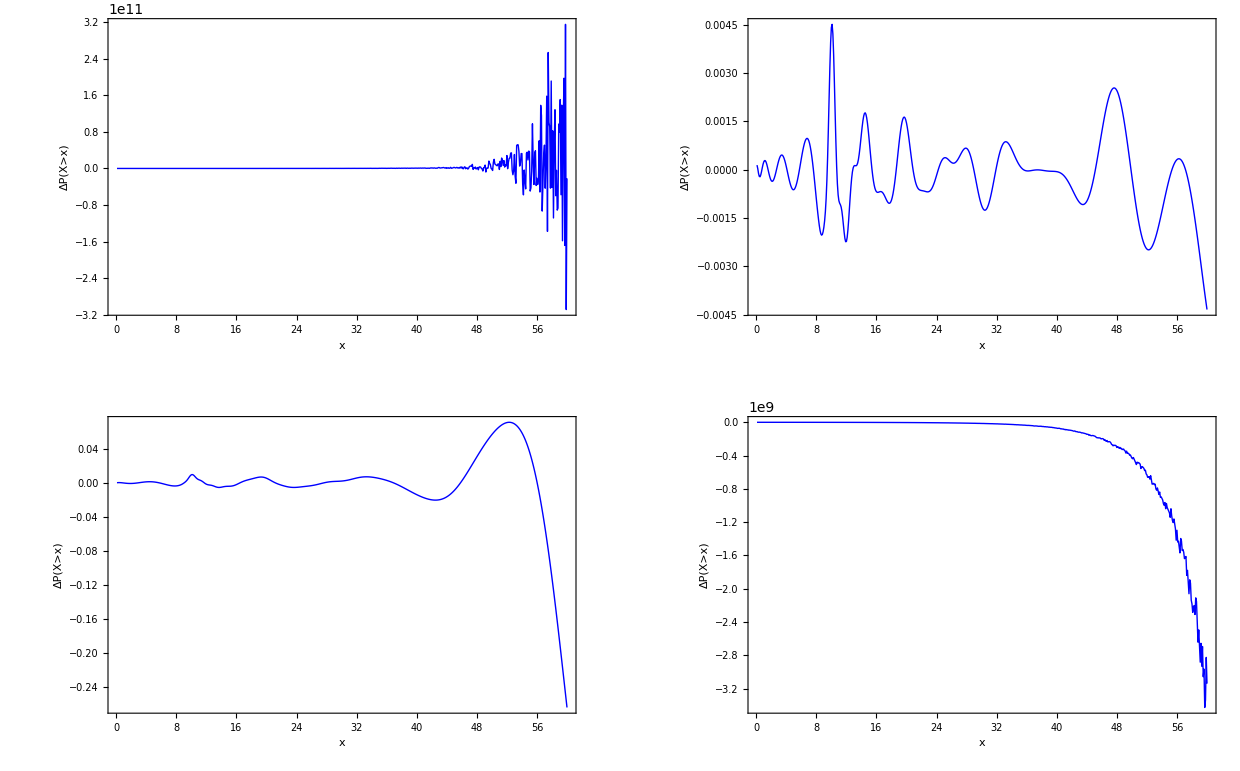

```mathematica
(*Fonction de survie pour différente paramétrisations comparaison avec Fourier*)
GraphicsGrid[{{DiscretePlot[(SurvivalCompoundPoissonUnifPolynomial[[1]]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Parametrization 1",24]}},ImageSize->Large,PlotStyle->Blue],
DiscretePlot[(SurvivalCompoundPoissonUnifPolynomial[[2]]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Parametrization 2",24]}},ImageSize->Large,PlotStyle->Blue]},
{DiscretePlot[(SurvivalCompoundPoissonUnifPolynomial[[3]]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Parametrization 3",24]}},ImageSize->Large,PlotStyle->Blue],
DiscretePlot[(SurvivalCompoundPoissonUnifPolynomial[[4]]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Parametrization 4",24]}},ImageSize->Large,PlotStyle->Blue]}
}]
```

```mathematica
(*Tableau fonction de survie et erreur relative sur la fonction de survie pour différentes paramétrisation du développement polynomiale*)
(*Fonction de survie*)
TeXForm[Table[{N[k],N[SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β]],N[SurvivalCompoundPoissonUnifPolynomial[[1]]/.u->k],N[SurvivalCompoundPoissonUnifPolynomial[[2]]/.u->k],N[SurvivalCompoundPoissonUnifPolynomial[[3]]/.u->k],N[SurvivalCompoundPoissonUnifPolynomial[[4]]/.u->k]},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{cccccc}
 6. & 0.811227 & 1.36315\times 10^7 & 0.811507 & 0.810796205618057 & -1.24518\times 10^6 \\
 12. & 0.56834 & 1.46801\times 10^7 & 0.567072 & 0.567464666324267 & -1.24518\times 10^6 \\
 18. & 0.34191 & 9.43718\times 10^6 & 0.341587 & 0.3434973122267232 & -1.24518\times 10^6 \\
 24. & 0.17857 & 1.04858\times 10^7 & 0.178539 & 0.1776357763563670 & -1.24518\times 10^6 \\
 30. & 0.081776 & 1.15343\times 10^7 & 0.0816851 & 0.0819529359662154 & -1.24518\times 10^6 \\
 36. & 0.033478 & 5.24288\times 10^6 & 0.0334768 & 0.03357644909155546 & -1.27795\times 10^6 \\
 42. & 0.0124404 & 1.57286\times 10^7 & 0.0124332 & 0.01219211758603841 & -1.24518\times 10^6 \\
 48. & 0.00420535 & 2.09715\times 10^6 & 0.00421571 & 0.00433441587318858 & -1.27795\times 10^6 \\
 54. & 0.00132527 & 4.29916\times 10^7 & 0.00132356 & 0.001403475357017921 & -1.21242\times 10^6 \\
 60. & 0.000386308 & -8.38861\times 10^6 & 0.000384629 & 0.000284102648171442 & -1.21242\times 10^6 \\
\end{array}
\right)

```mathematica
(*Erreur relative*)
TeXForm[Table[{N[k],N[Round[(N[SurvivalCompoundPoissonUnifPolynomial[[1]]/.u->k]-N[SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β]])/N[SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonUnifPolynomial[[2]]/.u->k]-N[SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β]])/N[SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonUnifPolynomial[[3]]/.u->k]-N[SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β]])/N[SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β]]*100*10^5]*10^-5],
N[Round[(N[SurvivalCompoundPoissonUnifPolynomial[[4]]/.u->k]-N[SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β]])/N[SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β]]*100*10^5]*10^-5]
},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{ccccc}
 6. & 1.68035\times 10^9 & 0.03449 & -0.05311 & -1.53494\times 10^8 \\
 12. & 2.58297\times 10^9 & -0.2231 & -0.15394 & -2.19092\times 10^8 \\
 18. & 2.76014\times 10^9 & -0.09454 & 0.4643 & -3.64185\times 10^8 \\
 24. & 5.87206\times 10^9 & -0.01759 & -0.52331 & -6.97308\times 10^8 \\
 30. & 1.41048\times 10^{10} & -0.11119 & 0.21631 & -1.52268\times 10^9 \\
 36. & 1.56607\times 10^{10} & -0.00353 & 0.29409 & -3.81729\times 10^9 \\
 42. & 1.26432\times 10^{11} & -0.05834 & -1.99604 & -1.00092\times 10^{10} \\
 48. & 4.98687\times 10^{10} & 0.24625 & 3.06909 & -3.03887\times 10^{10} \\
 54. & 3.24398\times 10^{12} & -0.1292 & 5.90079 & -9.14842\times 10^{10} \\
 60. & -2.17148\times 10^{12} & -0.43455 & -26.457 & -3.13847\times 10^{11} \\
\end{array}
\right)

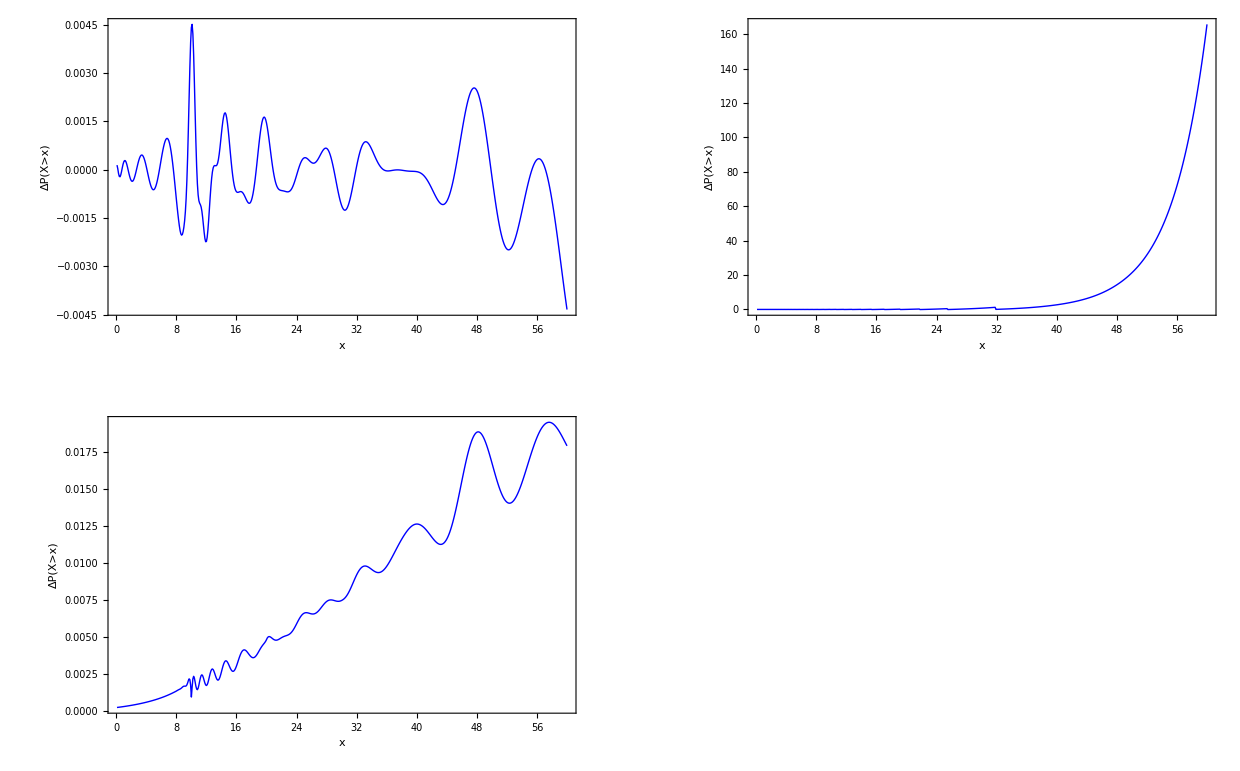

```mathematica
(*Comparaison de l'erreur sur la fonction de survie avec d'autres méthodes*)
GraphicsGrid[{
{DiscretePlot[(SurvivalCompoundPoissonUnifPolynomial[[2]]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Polynomial",24]}},ImageSize->Large,PlotStyle->Blue],
DiscretePlot[(SurvivalCompoundPoissonUnifMnats[λ,α,β,αMnats,bMnats,u]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Exponential Moments",24]}},ImageSize->Large,PlotStyle->Blue]},
{DiscretePlot[(SurvivalPoissonCompoundUnifPanger[VectProbaCompoundPoisson,h,u]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,u,nFFT,λ,α,β],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Panjer",24]}},ImageSize->Large,PlotStyle->Blue]}}]
```

```mathematica
(*Evaluation de la fonction de survie via différentes méthodes*)
TeXForm[Table[{k,SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β],N[SurvivalCompoundPoissonUnifPolynomial[[2]]/.u->k],SurvivalCompoundPoissonUnifMnats[λ,α,β,αMnats,bMnats,k],SurvivalPoissonCompoundUnifPanger[VectProbaCompoundPoisson,h,k]},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{ccccc}
 6 & 0.811227 & 0.811507 & 0.798633 & 0.811957 \\
 12 & 0.56834 & 0.567072 & 0.557872 & 0.569321 \\
 18 & 0.34191 & 0.341587 & 0.35222 & 0.343157 \\
 24 & 0.17857 & 0.178539 & 0.216235 & 0.179621 \\
 30 & 0.081776 & 0.0816851 & 0.140781 & 0.0823872 \\
 36 & 0.033478 & 0.0334768 & 0.0644221 & 0.0338055 \\
 42 & 0.0124404 & 0.0124332 & 0.0644221 & 0.0125867 \\
 48 & 0.00420535 & 0.00421571 & 0.0644221 & 0.00428459 \\
 54 & 0.00132527 & 0.00132356 & 0.0644221 & 0.00134572 \\
 60 & 0.000386308 & 0.000384629 & 0.0644221 & 0.000393232 \\
\end{array}
\right)

```mathematica
(*Ecart relatif à l'approximation obtenue par Fourier *)
TeXForm[Table[{k,N[Round[
((N[SurvivalCompoundPoissonUnifPolynomial[[2]]/.u->k]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β])*100*10^(5)]*10^(-5)],N[Round[((N[SurvivalCompoundPoissonUnifMnats[λ,α,β,αMnats,bMnats,k]]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β])*100*10^(5)]*10^(-5)],N[Round[((N[SurvivalPoissonCompoundUnifPanger[VectProbaCompoundPoisson,h,k]]-SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β])/SurvivalCompoundPoissonUnifFFT[mFFT,bFFT,k,nFFT,λ,α,β])*100*10^(5)]*10^(-5)]},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{cccc}
 6 & 0.03449 & -1.55242 & 0.08995 \\
 12 & -0.2231 & -1.84175 & 0.17261 \\
 18 & -0.09454 & 3.01549 & 0.36475 \\
 24 & -0.01759 & 21.0926 & 0.58869 \\
 30 & -0.11119 & 72.1542 & 0.74738 \\
 36 & -0.00353 & 92.4311 & 0.97826 \\
 42 & -0.05834 & 417.844 & 1.17585 \\
 48 & 0.24625 & 1431.91 & 1.88423 \\
 54 & -0.1292 & 4761.04 & 1.543 \\
 60 & -0.43455 & 16576.4 & 1.79229 \\
\end{array}
\right)

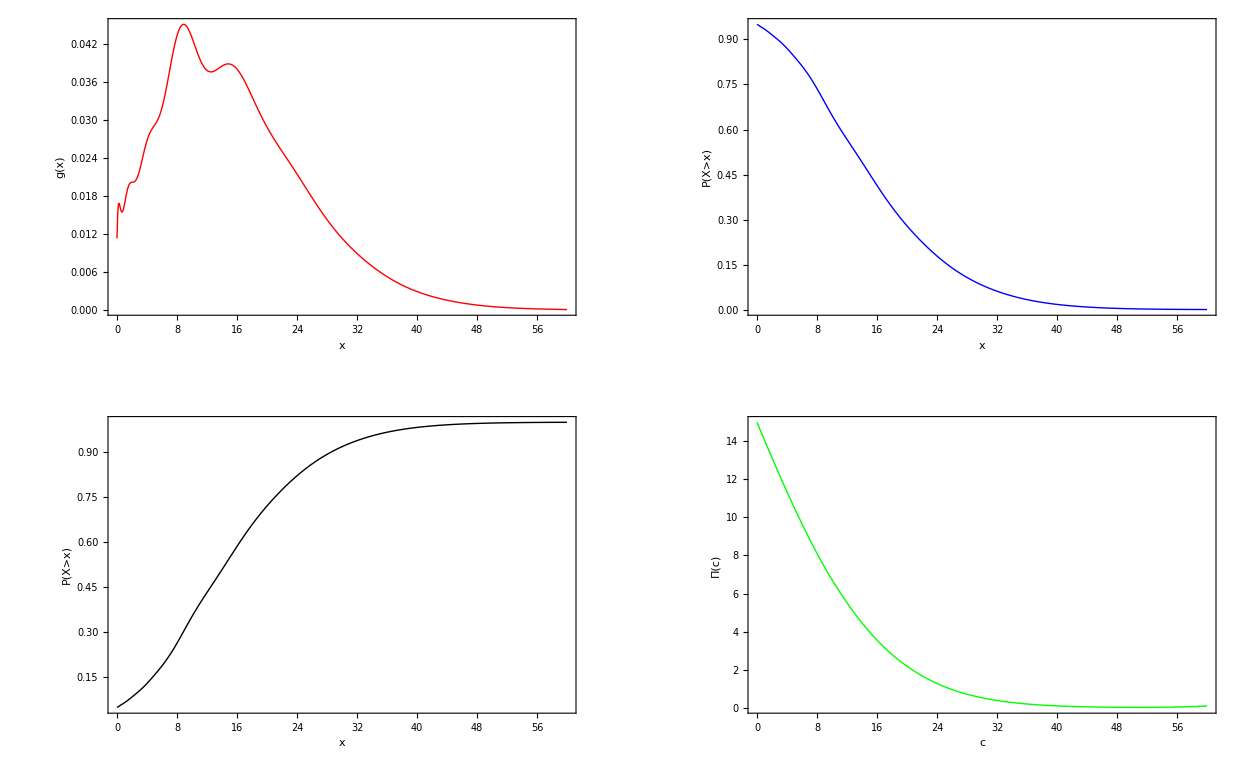

```mathematica
(*Approximation polynomial de la densité, de la fonction de survie et de la prime Stop Loss*)
GraphicsGrid[{{
DiscretePlot[DensityCompoundPoissonUnifPolynomial[[2]],{x,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,Filling->None,FrameLabel->{{Style["g(x)",24],None},{Style["x",24],Style["PDF",24]}},ImageSize->Large,PlotStyle->{Red,Thick}],
DiscretePlot[SurvivalCompoundPoissonUnifPolynomial[[2]],{u,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Filling->None,Joined->True,Filling->None,FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Survival Function",24]}},ImageSize->Large,PlotStyle->{Blue,Thick}]},
{
DiscretePlot[1-SurvivalCompoundPoissonUnifPolynomial[[2]],{u,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Filling->None,Joined->True,Filling->None,FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Survival Function",24]}},ImageSize->Large,PlotStyle->{Black,Thick}],
DiscretePlot[UsualStopLossCompoundPoissonUniformPolynomial,{c,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["Π(c)",24],None},{Style["c",24],Style["Usual Stop Loss Premium",24]}},ImageSize->Large,PlotStyle->{Green,Thick}]}}]
```

```mathematica
(*Stop Loss Premium par simulations*)
NObs=1000000;
SamplePoisson=RandomVariate[PoissonDistribution[λ],NObs];
SampleCompoundPoissonUniform=Table[Total[RandomVariate[UniformDistribution[{α,β}],SamplePoisson[[i]]]],{i,1,NObs,1}];
```

```mathematica
TeXForm[Table[{Retention,Mean[Table[Max[SampleCompoundPoissonUniform[[i]]-Retention,0],{i,1,NObs,1}]],N[UsualStopLossCompoundPoissonUniformPolynomial/.c->Retention],((N[UsualStopLossCompoundPoissonUniformPolynomial/.c->Retention]-Mean[Table[Max[SampleCompoundPoissonUniform[[i]]-Retention,0],{i,1,NObs,1}]])/Mean[Table[Max[SampleCompoundPoissonUniform[[i]]-Retention,0]  ,{i,1,NObs,1}]])*100},{Retention,0,umax,umax/10}]]
```

\left(
\begin{array}{cccc}
 0 & 14.9853 & 15. & 0.0980556 \\
 6 & 9.64871 & 9.66179 & 0.135476 \\
 12 & 5.50303 & 5.51476 & 0.213109 \\
 18 & 2.78782 & 2.79742 & 0.344321 \\
 24 & 1.26726 & 1.27289 & 0.444929 \\
 30 & 0.520103 & 0.523035 & 0.563808 \\
 36 & 0.194318 & 0.195566 & 0.642539 \\
 42 & 0.0661649 & 0.067064 & 1.3589 \\
 48 & 0.020686 & 0.0215882 & 4.36139 \\
 54 & 0.00594759 & 0.0203992 & 242.983 \\
 60 & 0.00162014 & 0.0835602 & 5057.6 \\
\end{array}
\right)

```mathematica
Variance[UniformDistribution[{aU,bU}]]/Mean[UniformDistribution[{aU,bU}]]
Mean[UniformDistribution[{aU,bU}]]^(2)/Variance[UniformDistribution[{aU,bU}]]
```

(-aU+bU)^2/(6 (aU+bU))

(3 (aU+bU)^2)/(-aU+bU)^2